# Audio L-Systems

## Following along

```mathematica
URLShorten["https://raw.githubusercontent.com/gvarnavi/generative-art-iap/master/01.25-Tuesday/04_audio-l-systems.nb"]
```

https://wolfr.am/11CaNIiw8

```mathematica
NotebookOpen["https://wolfr.am/11CaNIiw8"]
```

## Audio L-Systems

The symmetry and repetition found in L-Systems hints that they could be used to compose music.
This has been attempted a few different ways, most of which don’t sound good.

Peter Worth and Susan Stepney published a pleasing translation in their paper, “Growing Music: musical interpretations of L-Systems”

### Creating Rules

#### Visually:

F → move forward

X → null (do nothing)

2 → turn counter-clockwise by an angle θ

4 → turn clockwise by an angle θ

6 → save location

8 → return to saved location

#### Musically:

F → play pitch

X → null (do nothing)

2 → go up one note in the given key

4 → go down one note in the given key

6 → save pitch

### Generating Sheet Music

The music rules can be written in a format very similar to the one used for visual L-Systems

Given the following set of instructions:

```mathematica
nest[state_,rules_,iter_]:=Nest[Flatten[#/.rules]&,state,iter]
```

```mathematica
instructions=nest[{"X"},{"X"->{"F",6,4,"X",8,6,2,"X",8,"F","X"},"F"->{"F","F"}},3]
```

These instructions can be visualized as before:

```mathematica
visualizeLSystemPushPop[state_,rotAngle_,drawLetters_]:=(*doesn't assume rotation for push/pop*)Module[{currentAngle=0,currentLocation={0,0},currentState={},savedState={},savedAngle=0,savedLocation={0,0}},
(Switch[#,
6,savedState={savedAngle,savedLocation,savedState},
8,{savedAngle,savedLocation,savedState}=savedState,
_?(Or@@Thread[#==drawLetters]&),
currentState={currentState,Line@{savedLocation,savedLocation+={Cos@savedAngle,Sin@savedAngle}}}];
If[#==2||#==4,savedAngle+=I^# rotAngle])&/@state;
Graphics[Flatten@currentState,ImageSize->500]
]
```

```mathematica
visualizeLSystemPushPop[instructions, Pi/4, {"F"}]
```

And converted to “music”

```mathematica
rawConvertToMusic[state_,playLetters_]:=Module[{currentAngle=0,currentPitch=8,currentState={1},savedState={},savedAngle=0,savedPitch=8},
(Switch[#,
6,savedState={savedAngle,savedPitch,savedState},
8,{savedAngle,savedPitch,savedState}=savedState,
_?(Or@@Thread[#==playLetters]&),
currentState={currentState,savedPitch+savedAngle}];
If[#==2||#==4,savedAngle+=I^# ])&/@state;
Clip[#,{1,10}]&/@(Flatten@currentState)[[2;;]]
]
```

```mathematica
rawConvertToMusic[instructions, {"F"}]
```

```mathematica
ListPlot[rawConvertToMusic[instructions, {"F"}],Frame->True]
```

We can play this with Mathematica:

```mathematica
cMajor={None,"C3", "D3", "E3","F3", "G3","A3","B3","C4", "D4", "E4","F4", "G4", "A4", "B4", "C5"};
```

```mathematica
EmitSound[Sound[SoundNote[cMajor[[#]],0.5,"Cello"]]&/@rawConvertToMusic[instructions, {"F"}]]
```

Note: `EmitSound` will proceed to play the entire sequence unless interrupted by another `EmitSound` command.
As such, we define a simple ‘get-out-of-jail’ card

```mathematica
stopSound[]:=EmitSound[SoundNote[0]]
```

It’ll sound a lot better if we can combine long notes:

```mathematica
EmitSound[Sound[SoundNote[cMajor[[#]],0.5,"Cello"]]&/@{2,2,2,2}]
```

```mathematica
EmitSound[Sound[SoundNote[cMajor[[#]],2,"Cello"]]&/@{2}]
```

#### Cleaning up the Music

This function counts repeated F’s as held notes:

```mathematica
combineNotes[sequence_]:=Module[{currentPitch=1,tally=1,currentCombined={},paddedSequence},
paddedSequence=Append[sequence,1]; (*ensures that all notes are counted*)
Switch[#,
currentPitch, tally+=1,
_, AppendTo[currentCombined,{currentPitch, tally}];tally=1; currentPitch=#]&/@paddedSequence;
currentCombined]
```

The functions can be combined to make a general L-System player:

```mathematica
convertToSound[{note_, duration_},tempo_,instrument_:"Cello", key_:cMajor]:=
SoundNote[key[[note]],duration*60/tempo,instrument]
```

```mathematica
playSequence[sequence_,tempo_, instrument_:"Cello", key_:cMajor]:=Module[{rawSequence,combinedSequence},
rawSequence =rawConvertToMusic[sequence,{"F"}];
combinedSequence=combineNotes[rawSequence];
EmitSound[convertToSound[#,tempo, instrument, key]&/@combinedSequence]]
```

## A Few Tunes

### Koch Snowflake

```mathematica
kochSnowflake = nest[{"F",2,2,"F",2,2,"F"},{"F"->{"F",4,"F",2,2,"F",4,"F"}},2];
```

```mathematica
With[{str=SubstitutionSystem[{"F"->"F+F--F+F"},"F--F--F",3]},
GraphicsGrid[Partition[Graphics[Line@AnglePath[StringCases[#,{"F"->{1,0},"+"->{0,Pi/3},"-"->{0,-Pi/3}}]],ImageSize->500]&/@str,4],ImageSize->500]]
```

```mathematica
rawConvertToMusic[kochSnowflake,{"F"}]
```

```mathematica
playSequence[kochSnowflake, 120]
```

### Pythagoras Tree

```mathematica
pythagorasTree=nest[{"A"},{"B"->{"B","B"},"A"->{"B",6,2,"A",8,4,"A"}},6];
```

```mathematica
visualizeLSystemPushPop[nest[{"A"},{"B"->{"B","B"},"A"->{"B",6,2,"A",8,4,"A"}},6], π/4,{"A","B"}]
```

```mathematica
rawConvertToMusic[pythagorasTree,{"A","B"}]
```

```mathematica
playSequence[pythagorasTree/.{"A"->"F", "B"->"F"}, 1000]
```

### Branched Tree

```mathematica
branchedTree=nest[{"X"},{"X"->{"F",6,4,"X",8,6,2,"X",8,"F","X"},"F"->{"F","F"}},4];
```

#### --- start initialization code ---

```mathematica
stopSound[]:=EmitSound[SoundNote[0]]
```

```mathematica
visualizeLSystemPushPopLines[state_,rotAngle_,drawLetters_]:=Module[{currentAngle=0,currentLocation={0,0},currentState={},savedState={},savedAngle=0,savedLocation={0,0},allLines, relevantPoints,betterLines},
(Switch[#,6,savedState={savedAngle,savedLocation,savedState},8,
{savedAngle,savedLocation,savedState}=savedState,_?(Or@@Thread[#==drawLetters]&),currentState={currentState,Line@{savedLocation,savedLocation+={Cos@savedAngle,Sin@savedAngle}}}];
If[#==2||#==4,savedAngle+=I^# (rotAngle+0.001)])&/@state;
allLines=Flatten@currentState;
relevantPoints=Flatten[allLines[[#,1]]&/@Range[1, Length@allLines],1];
(*get rid of repeats*)
betterLines=Split[Union/@Partition[combineLines[relevantPoints],2,1]][[All,1]];
(*finally, delete any consecutive lines with the same slope*)
Quiet[If[slope[betterLines[[#]]]==
slope[betterLines[[#-1]]], betterLines=Delete[betterLines, #],Nothing
]&/@Range[2,(Length@betterLines)]];
Line/@betterLines
]
```

```mathematica
combineLines[pointsSequence_]:=Module[{combined=pointsSequence[[;;2]]},
Which[
(*case for the same point*)
#==combined[[-1]], combined=combined,

(*case for the same non-vertical slope*)
(slope[#, combined[[-1]]]==slope[combined[[-1]], combined[[-2]]])&&
(#[[1]]-combined[[-1,1]])*(combined[[-1,1]]-combined[[-2,1]])>=0, combined = ReplacePart[combined, (-1)->#],

(*case otherwise*)
True, combined=Append[combined, #];
]&/@(pointsSequence[[2;;]]);
combined
]
```

```mathematica
slope[{x1_,y1_},{x2_,y2_}]:=Which[x2==x1,100,True,(y2-y1)/(x2-x1)];
slope[{{x1_,y1_},{x2_,y2_}}]:=Which[x2==x1,100,True,(y2-y1)/(x2-x1)];
```

#### --- end initialization code ---

```mathematica
Graphics@visualizeLSystemPushPopLines[branchedTree, π/4,{"F"}]
```

```mathematica
playSequence[branchedTree,400]
```

## Variations on Musical L-Systems

### Visualization

```mathematica
drawLines={Line[{{0,0},{0,0}}]};
```

```mathematica
Dynamic[
Graphics[drawLines, PlotRange->{{0,35},{-15,15}}]]
```

#### --- start initialization code ---

```mathematica
writeSequence[sequence_,tempo_, instrument_:"Cello", key_:cMajor]:=Module[{rawSequence,combinedSequence},
rawSequence =rawConvertToMusic[sequence,{"F"}];
combinedSequence=combineNotes[rawSequence];
convertToSound[#,tempo, instrument, key]&/@(combinedSequence[[2;;]])]
```

```mathematica
playSequence[sequence_,tempo_, instrument_:"Cello", key_:cMajor]:=Module[{rawSequence,combinedSequence},
rawSequence =rawConvertToMusic[sequence,{"F"}];
combinedSequence=combineNotes[rawSequence];
EmitSound[convertToSound[#,tempo, instrument, key]&/@(combinedSequence[[2;;]])]]
```

```mathematica
soundAndGraphic[sequence_,tempo_,angle_,instrument_:"Cello", key_:cMajor]:=DynamicModule[{combinedSequence,durations,linesWithSound},
linesWithSound=visualizeLSystemPushPopLines[sequence,angle,{"F"}];
combinedSequence=writeSequence[sequence, tempo, instrument, key];
durations=combineNotes[rawConvertToMusic[sequence,{"F"}]][[2;;,2]];
i=1;
Quiet@Do[
EmitSound[combinedSequence[[i]]];drawLines=linesWithSound[[;;i+1]];
Pause[durations[[i]]*60/tempo+0.02];
i+=1;,(Length@linesWithSound-1)];
]
```

#### --- end initialization code ---

```mathematica
soundAndGraphic[branchedTree, 800, Pi/4];
```

### “Symphonies”: multiple parts

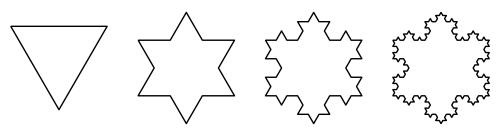

```mathematica
cello=nest[{"F",2,2,"F",2,2,"F"},{"F"->{"F",4,"F",2,2,"F",4,"F"}},1];
viola=nest[{"F",2,2,"F",2,2,"F"},{"F"->{"F",4,"F",2,2,"F",4,"F"}},2];
violin=nest[{"F",2,2,"F",2,2,"F"},{"F"->{"F",4,"F",2,2,"F",4,"F"}},3];
```

```mathematica
violinKey={None,"C4", "D4", "E4","F4", "G4","A4","B4", "C5", "D5", "E5","F5", "G5","A5","B5","C6", "D6", "E6","F6", "G6", "A6" "B6", "C7"};

violaKey={None,"A3","B3","C4", "D4", "E4","F4", "G4","A4","B4","C5", "D5", "E5","F5", "G5","A5","B5","C6", "D6", "E6","F6", "G6", "A6"};

celloKey={None,"A1","B1","C2", "D2", "E2","F2", "G2","A2","B2","C3", "D3", "E3","F3", "G3", "A3", "B3", "C4", "D4", "E4", "F4", "G4", "A4"};
```

#### --- start initialization code ---

```mathematica
combineNotesSymphony[sequence_]:=Module[{currentPitch=1,beginning=1,end=1,currentCombined={},paddedSequence},
paddedSequence=Append[sequence,1]; (*ensures that all notes are counted*)
Switch[#,
currentPitch, end+=1,
_, AppendTo[currentCombined,{currentPitch, {beginning,end}}];beginning=end;end+=1;currentPitch=#]&/@paddedSequence;
currentCombined]
```

```mathematica
sequenceSymphony[sequence_,tempo_, instrument_:"Cello", key_:cMajor]:=Module[{rawSequence,combinedSequence},
rawSequence =rawConvertToMusic[sequence,{"F"}];
combinedSequence=combineNotesSymphony[rawSequence];
(convertToSound[#,tempo, instrument, key]&/@combinedSequence)]
```

#### --- end initialization code ---

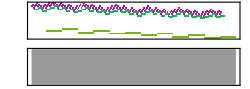

```mathematica
Sound@Join[
(sequenceSymphony[violin,400,"Violin", violinKey]),(sequenceSymphony[viola,100, "Viola", violaKey]),(sequenceSymphony[cello,25,"Cello", celloKey])]
```